1/6 λ (6+3 λ-4 λ^2)

1/6 λ (30+15 λ-8 λ^2)

1/6 λ (-6-3 λ+16 λ^2)

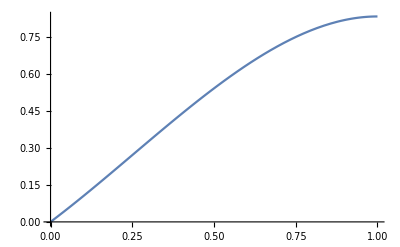

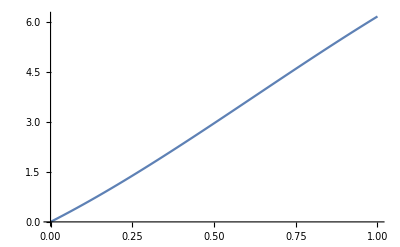

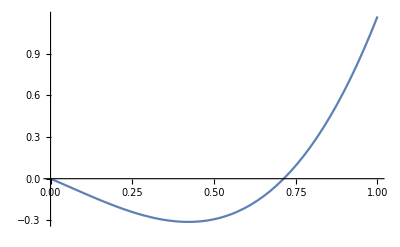

```mathematica
AEDM = 8/5(Sqrt[(1-λ)](1+4λ))/(5+5λ-4(λ^2));
(*Plot[AEDM,{λ,0,1}]*)
n=1/(4Pi)2(1-λ)(5+5λ-4λ^2)/3;

Simplify[n];
(*Plot[n,{λ,0,1}]*)
Integrate[n, λ, Assumptions->λ∈Reals&&λ>=0];
Integrate[n, {λ,0,1}, Assumptions->λ∈Reals&&λ>=0];
(*γ=29.3;*)
(*ϕ=0.1;*)
d=((1-λ)(2λ+1)Sin[ϕ])/(γ((5+5λ-4λ^2)+(8λ^2-λ-1)Cos[ϕ]));
CForm[d];
FullSimplify[%];
(*Plot[d,{λ,0,1}]*)
Integrate[d, λ, Assumptions->{λ,γ}∈Reals&&λ>=0];
A1 = 1/6 λ(-4λ^2+3 λ+6)
A2=1/6 λ(-8 λ^2+15 λ+30)
A3=1/6 λ(16 λ^2-3 λ-6)
Plot[A1,{λ,0,1}]
Plot[A2,{λ,0,1}]
Plot[A3,{λ,0,1}]
```

```mathematica
-1/(16 γ (1-2 Cos[ϕ])^2)(8 λ (-1+2 Cos[ϕ])+(√6 ArcTanh[(√(2/3) (5-8 λ+(-1+16 λ) Cos[ϕ]))/(√(81-124 Cos[ϕ]+11 Cos[2 ϕ]))] (-9+8 Cos[ϕ]+17 Cos[2 ϕ]))/(√(81-124 Cos[ϕ]+11 Cos[2 ϕ]))-3 (1+Cos[ϕ]) Log[5+5 λ-4 λ^2+(-1-λ+8 λ^2) Cos[ϕ]]) Sin[ϕ]
```

(5 λ-3 λ^3+λ^4)/(6 π)

(5*λ - 3*Power(λ,3) + Power(λ,4))/(6.*Pi)